```mathematica
Quit
```

```mathematica
$Assumptions=m>0&&τ>0&&k>0&&T>0&&m∈Reals&&τ∈Reals
```

m>0&&τ>0&&k>0&&T>0&&m∈ℝ&&τ∈ℝ

Distribución de Maxwell para la rapidez

```mathematica
PM[v_]:=4π(m/(2π k T))^(3/2)Exp[-(m v^2)/(2k T)] v^2
```

Confirmando la normalización

```mathematica
Integrate[PM[v],{v,0,Infinity}]
```

1

En términos de τ=k T

```mathematica
PM[v_,m_,τ_]:=4π(m/(2π τ))^(3/2)Exp[-(m v^2)/(2τ)] v^2
```

Gráficas para frío τ=10 (azul), intermedio τ=20 (naranja) y más caliente τ=30 (verde)

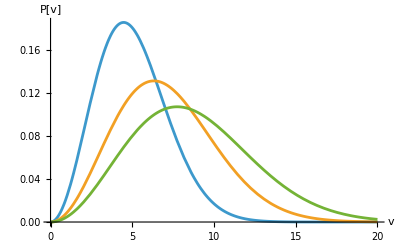

```mathematica
Plot[{PM[v,1,10],PM[v,1,20],PM[v,1,30]},{v,0,20},AxesLabel->{"v","P[v]"}]
```

Rapidez máxima

```mathematica
D[PM[v,m,τ],v]//Simplify
```

-(ⅇ^(-(m v^2)/(2 τ)) m^(3/2) √(2/π) v (m v^2-2 τ))/τ^(5/2)

```mathematica
vmax[m_,τ_]=Sqrt[(2τ)/m]
```

√2 √(τ/m)

Rapidez promedio <v>

```mathematica
Integrate[v PM[v,m,τ],{v,0,Infinity}]//Simplify//Refine
```

2 √(2/π) √(τ/m)

```mathematica
vmean[m_,τ_]=2 √(2/π) √(τ/m)
```

2 √(2/π) √(τ/m)

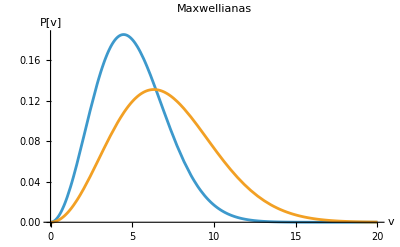

```mathematica
Plot[{PM[v,1,10],PM[v,1,20]},{v,0,20},GridLines->{{vmax[1,10],vmean[1,10],vmax[1,20],vmean[1,20]}},PlotLabel->"Maxwellianas",AxesLabel->{"v","P[v]"}]
```

Raiz cuadrática media Sqrt[<v^2>]

```mathematica
(Integrate[v^2 PM[v,m,τ],{v,0,Infinity}])^(1/2)//Simplify//Refine
```

√3 √(τ/m)

Las tres velocidades características vmax, <v>, √(<v^2>) son del mismo orden, pues van como  la raiz cuadrada de la temperatura (T)^(1/2)